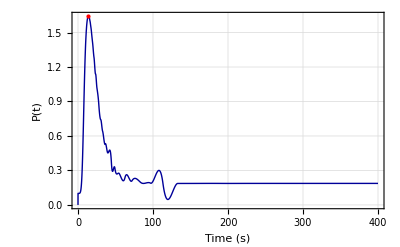

```mathematica
(*Parámetros*)TT=3*10^4;
x0Original={TT,5*10^4,0,0,0,0,0,0,0,0,0};

opts={AccuracyGoal->6,PrecisionGoal->6,Method->"StiffnessSwitching"};

tspan=Range[0.0,400,0.05];

(*Asignamos nombres descriptivos a los parámetros*){kon,koff,kp,phi,gammaPos,lambda,delta,YT,PT,mu,gammaNeg}={1*10^-5,0.05,0.04,0.04,1,100,100,100,2.5,500,500};

(*Definimos x como vector de 11 funciones de t*)
xVars=Array[x,11];
ODELimIFF1=Table[D[xVars[[i]][t],t]==Switch[i,1,-kon*xVars[[1]][t]*xVars[[2]][t]+koff*Total[Table[xVars[[j]][t],{j,3,9}]],2,-kon*xVars[[1]][t]*xVars[[2]][t]+koff*Total[Table[xVars[[j]][t],{j,3,9}]],3,kon*xVars[[1]][t]*xVars[[2]][t]-(koff+kp)*xVars[[3]][t],4,kp*xVars[[3]][t]-(koff+kp)*xVars[[4]][t],5,kp*xVars[[4]][t]-(koff+kp)*xVars[[5]][t],6,kp*xVars[[5]][t]-(koff+kp)*xVars[[6]][t],7,kp*xVars[[6]][t]-(koff+kp)*xVars[[7]][t],8,kp*xVars[[7]][t]-(koff+phi)*xVars[[8]][t],9,phi*xVars[[8]][t]-koff*xVars[[9]][t],10,gammaPos*(YT-xVars[[10]][t])-gammaNeg*xVars[[10]][t]+lambda*xVars[[8]][t]*(YT-xVars[[10]][t]),11,gammaPos*(PT-xVars[[11]][t])-gammaNeg*xVars[[11]][t]+delta*xVars[[10]][t]*(PT-xVars[[11]][t])-mu*xVars[[8]][t]*xVars[[11]][t]],{i,11}];


initialConditions=Table[xVars[[i]][0]==x0Original[[i]],{i,11}];

(*Resolver*)
sol=NDSolveValue[Join[ODELimIFF1,initialConditions],xVars,{t,0,400},opts];

(*Extraer valores de la variable 7*)
x7values=Table[{tval,sol[[11]][tval]},{tval,tspan}];

(*Encontrar máximo*)
{tMax,yMax}=First@MaximalBy[x7values,Last];

(*Graficar*)
ListLinePlot[x7values,PlotStyle->{Thick,RGBColor[0,0,0.6]},Epilog->{Red,PointSize[Medium],Point[{tMax,yMax}]},GridLines->Automatic,Frame->True,FrameLabel->{"Time (s)","P(t)"},LabelStyle->Directive[12],PlotRange->All,Background->White]
```